```mathematica
(* Shooting Method for Solving Differential eq.s*)
(*1:- Can be used to Solve Boundary value Problems.
2:- By Shooting Method B.V problem becomes iniatial Value Problem.  *)
```

```mathematica
(* Using Shooting Method 
=>From Shooting point we shoot the values of dep. variable at varying shooting Angles.
(*Special Remarks about Shooting Method : in mathematica Shooting method can be implemented by Using NDSolve[] Commandand due to its pure function Solutions property. 
(* Points for converting a B.V problem into an iniatial value Problem.
1:- List out the B.C or  boundary points.
2:- decide shooting and target point out of the boundary points.
3:- determine the shooting angle or shooting slope at the shooting point such that u sucessfully hit the target. *)
```

```mathematica
Note: (* Tan[Shooting angle]= Shooting Slope= Gradient  ,,,,, e.g  y'[shooting point].
4:- Thus the B.V problem will also become an initial value problem.*)
Example:- solve the differential eq. : x''[t]+ω^2 x[t]==0, by using Shooting method.The B.c are ;x[0]=2;x[T]=2;
(* Solution *)
```

```mathematica
(*we decided that, t=0 is shooting point and t=T is a Target point. Here Shooting Angle can be found by NDSolve[].*)
```

```mathematica
(*Def. Trajectory as a function of unknown parameter ,i.e the shooting slope.*)
ω=20;deq= x''[t]+ω^2 x[t]==0;
xend[m_]:=x[1]/.NDSolve[{deq,x[0]==1,x'[0]==m},x,{t,0,1}][[1]];(*initial conditions.*)
Plot[xend[m],{m,-0.1,0.1}];
Do[if[Abs[xend[m]-1]<0.00001,slope=m,Print["m=",m]],{m,-0.1,0.1,0.001}];(*Abs[xend[m]-2]<0.00001? . Ans: it may not hit the target,that's why we use threashold value.  *)
```

m=-0.1

m=-0.099

m=-0.098

m=-0.097

m=-0.096

m=-0.095

m=-0.094

m=-0.093

m=-0.092

m=-0.091

m=-0.09

m=-0.089

m=-0.088

m=-0.087

m=-0.086

m=-0.085

m=-0.084

m=-0.083

m=-0.082

m=-0.081

m=-0.08

m=-0.079

m=-0.078

m=-0.077

m=-0.076

m=-0.075

m=-0.074

m=-0.073

m=-0.072

m=-0.071

m=-0.07

m=-0.069

m=-0.068

m=-0.067

m=-0.066

m=-0.065

m=-0.064

m=-0.063

m=-0.062

m=-0.061

m=-0.06

m=-0.059

m=-0.058

m=-0.057

m=-0.056

m=-0.055

m=-0.054

m=-0.053

m=-0.052

m=-0.051

m=-0.05

m=-0.049

m=-0.048

m=-0.047

m=-0.046

m=-0.045

m=-0.044

m=-0.043

m=-0.042

m=-0.041

m=-0.04

m=-0.039

m=-0.038

m=-0.037

m=-0.036

m=-0.035

m=-0.034

m=-0.033

m=-0.032

m=-0.031

m=-0.03

m=-0.029

m=-0.028

m=-0.027

m=-0.026

m=-0.025

m=-0.024

m=-0.023

m=-0.022

m=-0.021

m=-0.02

m=-0.019

m=-0.018

m=-0.017

m=-0.016

m=-0.015

m=-0.014

m=-0.013

m=-0.012

m=-0.011

m=-0.01

m=-0.009

m=-0.008

m=-0.007

m=-0.006

m=-0.005

m=-0.004

m=-0.003

m=-0.002

m=-0.001

m=0.

m=0.001

m=0.002

m=0.003

m=0.004

m=0.005

m=0.006

m=0.007

m=0.008

m=0.009

m=0.01

m=0.011

m=0.012

m=0.013

m=0.014

m=0.015

m=0.016

m=0.017

m=0.018

m=0.019

m=0.02

m=0.021

m=0.022

m=0.023

m=0.024

m=0.025

m=0.026

m=0.027

m=0.028

m=0.029

m=0.03

m=0.031

m=0.032

m=0.033

m=0.034

m=0.035

m=0.036

m=0.037

m=0.038

m=0.039

m=0.04

m=0.041

m=0.042

m=0.043

m=0.044

m=0.045

m=0.046

m=0.047

m=0.048

m=0.049

m=0.05

m=0.051

m=0.052

m=0.053

m=0.054

m=0.055

m=0.056

m=0.057

m=0.058

m=0.059

m=0.06

m=0.061

m=0.062

m=0.063

m=0.064

m=0.065

m=0.066

m=0.067

m=0.068

m=0.069

m=0.07

m=0.071

m=0.072

m=0.073

m=0.074

m=0.075

m=0.076

m=0.077

m=0.078

m=0.079

m=0.08

m=0.081

m=0.082

m=0.083

m=0.084

m=0.085

m=0.086

m=0.087

m=0.088

m=0.089

m=0.09

m=0.091

m=0.092

m=0.093

m=0.094

m=0.095

m=0.096

m=0.097

m=0.098

m=0.099

m=0.1

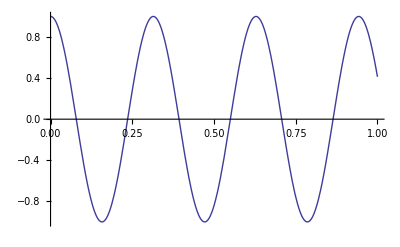

```mathematica
shootSol=x[t]/.NDSolve[{deq,x[0]==1,x'[0]==slope},x,{t,0,1}][[1]];
Plot[shootSol,{t,0,1}]
```